```mathematica
Needs["NDSolve`FEM`"]
```

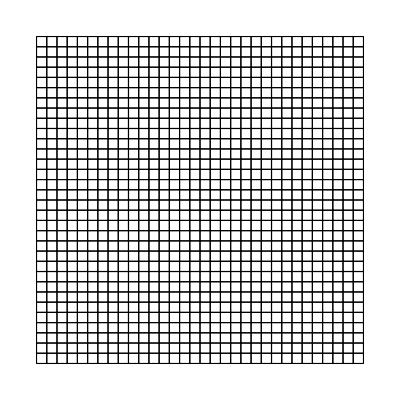

{{-p[x,y]+(u^(1,0)[x,y])/re,(u^(0,1)[x,y])/re},{(v^(1,0)[x,y])/re,-p[x,y]+(v^(0,1)[x,y])/re}}

(v[x,y] u^(0,1)[x,y]-(u^(0,2)[x,y])/re+p^(1,0)[x,y]+u[x,y] u^(1,0)[x,y]-(u^(2,0)[x,y])/re
p^(0,1)[x,y]+v[x,y] v^(0,1)[x,y]-(v^(0,2)[x,y])/re+u[x,y] v^(1,0)[x,y]-(v^(2,0)[x,y])/re)

{v[x,y] u^(0,1)[x,y]-(u^(0,2)[x,y])/re+p^(1,0)[x,y]+u[x,y] u^(1,0)[x,y]-(u^(2,0)[x,y])/re,p^(0,1)[x,y]+v[x,y] v^(0,1)[x,y]-(v^(0,2)[x,y])/re+u[x,y] v^(1,0)[x,y]-(v^(2,0)[x,y])/re,v^(0,1)[x,y]+u^(1,0)[x,y]}

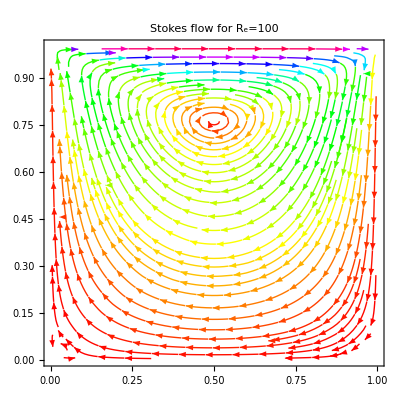

{NDSolve`StateData[<SteadyState>]}

NDSolve`StateData::argr: NDSolve`StateData called with 1 argument; 11 arguments are expected.

{NDSolve`StateData[< SteadyState >]}

{DegreesOfFreedom,ElementMesh,IncidentGroups,IncidentOffsets,Incidents,IntegrationOrder,InterpolationOrder,Precision,Properties,SolutionData,TotalDegreesOfFreedom,VariableData}

{DegreesOfFreedom,ElementMesh,IncidentOffsets,Incidents,IntegrationOrder,InterpolationOrder,Precision,Properties,SolutionData,TotalDegreesOfFreedom,VariableData}

{0,1089,4290,7491}

{0,1089,4290,7491}

Part::partd: Part specification vd⟦3⟧ is longer than depth of object.

MapThread::mptd: Object vd⟦3⟧ at position {2, 1} in MapThread[#1→{#2}&,{vd⟦3⟧,{1;;1089,1090;;4290,4291;;7491}}] has only 0 of required 1 dimensions.

MapThread[#1→{#2}&,{vd⟦3⟧,{1;;1089,1090;;4290,4291;;7491}}]

{p→{1;;1089},u→{1090;;4290},v→{4291;;7491}}

```mathematica
Ω=Rectangle[{0,0},{a,b}]/. {a->1,b->1};
RegionPlot[Ω,AspectRatio->Automatic];
mesh=ToElementMesh[Ω,"MaxCellMeasure"->1/1000,"MeshElementType"->QuadElement];
mesh["Wireframe"]
uv={u[x,y],v[x,y]};pxy=p[x,y];
σ=-pxy IdentityMatrix[2]+2/re Outer[D,uv,{x,y}]*1/2
NS = ∇_{x,y} uv. uv - ∇_{x,y} .σ;
MatrixForm[NS]
NSOperator = {NS, ∇_{x,y} .uv} // Flatten
bcs={DirichletCondition[{u[x,y]==1,v[x,y]==0.},y==1],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},x==1],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},y==0],DirichletCondition[{u[x,y]==0.,v[x,y]==0.},x==0],DirichletCondition[p[x,y]==0.,y==1&&x==1]};
StokesOperator=NSOperator/. {u[x,y]->0,v[x,y]->0};
pde=StokesOperator=={0,0,0}/. re->100;
{u0,v0,p0}=NDSolveValue[{pde,bcs},{u,v,p},{x,y}∈mesh,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"IntegrationOrder"->5}];
stokes=StreamPlot[{u0[x,y],v0[x,y]},{x,0,1},{y,0,1},StreamPoints->Fine,StreamColorFunction->Hue,StreamColorFunctionScaling->False,PlotLabel->Style["Stokes flow for \!\(\*SubscriptBox[\(R\), \(e\)]\)=100",Black,FontFamily->"Times",Bold]]
pde=StokesOperator=={0,0,0}/. re->100;
{state}=NDSolve`ProcessEquations[{pde,bcs},{u,v,p},{x,y}∈mesh,Method->{"FiniteElement","InterpolationOrder"->{u->2,v->2,p->1},"IntegrationOrder"->5}]
{NDSolve`StateData["<" "SteadyState" ">"]}
state["FiniteElementData"]["FEMMethodData"]["Properties"]

{"DegreesOfFreedom","ElementMesh","IncidentOffsets","Incidents","IntegrationOrder","InterpolationOrder","Precision","Properties","SolutionData","TotalDegreesOfFreedom","VariableData"}
offset=state["FiniteElementData"]["FEMMethodData"]["IncidentOffsets"]

{0,1089,4290,7491}
split=MapThread[#1->{#2}&,{vd[[3]],Span@@@Transpose[{Most[#+1],Rest[#]}&[offset]]}]

{p->{1;;1089},u->{1090;;4290},v->{4291;;7491}}
```